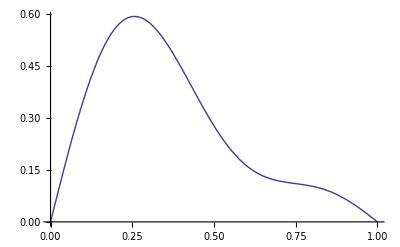
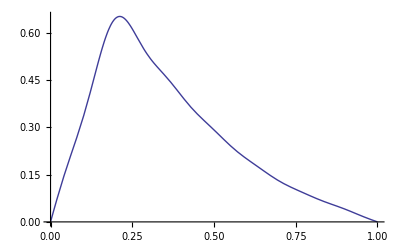
Behavior of N’th Fourier Sub Sum
      Let, u_0(x) = x(1-x) , u1(x) = x , l = 1;
      Then, a_n= (4(1-(-1)^n))/(n^3 π^3) , b_n = (-2 (nπ(-1))^n)/(n^2 π^2) 
      The N’th Fourier Sum will be, 
      	u_N= ∑_(n=1)^∞ (sin(nπx) ( (4(1-(-1)^n))/(n^3 π^3)cos( nπc t) +1/nπc(-2 (nπ(-1))^n)/(n^2 π^2) sin (nπc t )))
      	    = ∑_(n=1)^∞ (sin(nπx) ( (4(1-(-1)^n))/(n^3 π^3)cos( nπc t) -(2  (-1)^n)/(n^2 π^2 c) sin (nπc t )))
     Below u_N has been plotted..
     -Graphics-
     			  c = 0.2 , t=4 , N = 3,l = 1
       -Graphics-
       			 c = 0.2 , t=4 , N = 15, l = 1
       			 
     xϵ[0,1]^sup | u_M(x,t)- u_N(x,t)| 
     =  xϵ[0,1]^sup | ∑_(n=N)^M (sin(nπx) ( (4(1-(-1)^n))/(n^3 π^3)cos( nπc t) -(2   (-1)^n)/(n^2 π^2 c) sin (nπc t ))) |
     ≤    | ∑_(n=N)^M (4(1-(-1)^n))/(n^3 π^3)| + |∑_(n=N)^M (2   (-1)^n)/(n^2 π^2 c) | < ∞
     ∑_(n=1)^∞ 1/n^3 and ∑_(n=1)^∞ 1/n^2  are both bounded.
     So, as M⟶∞ , the margin of error ⟶ 0.
     So, the Formal Solution converges uniformly to the actual solution with higher speed.